# 自定函式

## Set working directory

```mathematica
Off[General::spell1];
Off[General::spell];$HistoryLimit=0;
FilePath="E:\\Mathemetica";
SetDirectory[FilePath]
```

E:\Mathemetica

## General Function

### Rad To Deg (*自訂一個函式 徑度 轉 角度*)

```mathematica
RadToDeg[Rad_]:=Module[{deg},    
deg=Rad/π*180.0;
Return[deg];
];
```

```mathematica
(* Rad_代表Rad是函式的引數， ":=" 代表現在要定義一個函式*)
```

```mathematica
(*Module這個函數第一個參數填的是需要宣告的變數(亦可給予初始值)，這邊填寫了deg代表函式內有deg這個變數，最後Return deg得值後deg這個變數的生命週期也就結束了，代表deg這個變數在函式外面找不到*)
```

# 1. Positions for a Four-Bar Mechanism

### Four-bar linkanges

-Graphics-

## 1.1 Parameters

### Bar lengths

```mathematica
Subscript[l, 1]=1.0;
Subscript[l, 2]=2.0;
Subscript[l, 3]=3.5;
Subscript[l, 4]=4.0;
Subscript[l, 7]=2.0;
Subscript[l, 8]=1.0;
```

### Angle 1

```mathematica
vtheta1=0Degree;
```

### Input Angle

```mathematica
vtheta2=120Degree;
```

### Link position

```mathematica
r1=Subscript[l, 1]*{Cos[Subscript[θ, 1]],Sin[Subscript[θ, 1]]};(*因為r1為一個向量，所以使用 { } 做為括號代表不只有一個維度或一個值*)
r2=Subscript[l, 2]*{Cos[Subscript[θ, 2]],Sin[Subscript[θ, 2]]};
r3=Subscript[l, 3]*{Cos[Subscript[θ, 3]],Sin[Subscript[θ, 3]]};
r4=Subscript[l, 4]*{Cos[Subscript[θ, 4]],Sin[Subscript[θ, 4]]};
r7=Subscript[l, 7]*{Cos[Subscript[θ, 7]],Sin[Subscript[θ, 7]]};
r8=Subscript[l, 8]*{Cos[Subscript[θ, 8]],Sin[Subscript[θ, 8]]};
r6=r7+r8;
```

## 1.2 Calculate angle 4 (先以變數代替定值因為之後會用到不同參數)

### Contants

```mathematica
AA=2 Cos[Subscript[θ, 1]] Subscript[l, 1] Subscript[l, 4]-2 Cos[Subscript[θ, 2]] Subscript[l, 2] Subscript[l, 4]
```

8. Cos[θ_1]-16. Cos[θ_2]

```mathematica
BB=2 Sin[Subscript[θ, 1]] Subscript[l, 1] Subscript[l, 4]-2 Sin[Subscript[θ, 2]] Subscript[l, 2] Subscript[l, 4]
```

8. Sin[θ_1]-16. Sin[θ_2]

```mathematica
CC=Subscript[l, 1]^2+Subscript[l, 2]^2+Subscript[l, 4]^2-Subscript[l, 3]^2-2 Cos[Subscript[θ, 1]-Subscript[θ, 2]] Subscript[l, 1] Subscript[l, 2]
```

8.75-4. Cos[θ_1-θ_2]

```mathematica
Index=-1;(*-1/1*)
```

```mathematica
tt=1/(CC-AA)(-BB+Index*√(BB^2-CC^2+AA^2))
```

(-8. Sin[θ_1]-√(-(8.75-4. Cos[θ_1-θ_2])^2+(8. Cos[θ_1]-16. Cos[θ_2])^2+(8. Sin[θ_1]-16. Sin[θ_2])^2)+16. Sin[θ_2])/(8.75-8. Cos[θ_1]-4. Cos[θ_1-θ_2]+16. Cos[θ_2])

### Angle 4

```mathematica
theta4=2 ArcTan[tt]
```

2 ArcTan[(-8. Sin[θ_1]-√(-(8.75-4. Cos[θ_1-θ_2])^2+(8. Cos[θ_1]-16. Cos[θ_2])^2+(8. Sin[θ_1]-16. Sin[θ_2])^2)+16. Sin[θ_2])/(8.75-8. Cos[θ_1]-4. Cos[θ_1-θ_2]+16. Cos[θ_2])]

```mathematica
vtheta4=theta4/.{Subscript[θ, 1]->vtheta1,Subscript[θ, 2]->vtheta2 };
(* /. 為"應用"後面這個對應值的意思 Subscript[但不是改變θ, 1]、Subscript[θ, 2] 值*)
(* 有點類似C語言使用的格式化輸出， printf("a + b = %d",a+b)   *)
RadToDeg[%](* % 為上一個運算結果的值，有點類似我們班當時團購機算機上面的Ans*)
```

79.63

```mathematica
RadToDeg[theta4]
```

114.592 ArcTan[(-8. Sin[θ_1]-√(-(8.75-4. Cos[θ_1-θ_2])^2+(8. Cos[θ_1]-16. Cos[θ_2])^2+(8. Sin[θ_1]-16. Sin[θ_2])^2)+16. Sin[θ_2])/(8.75-8. Cos[θ_1]-4. Cos[θ_1-θ_2]+16. Cos[θ_2])]

## 1.3 Calculate angle 3(先以變數代替定值因為之後會用到不同參數)

### Position 3

```mathematica
vr3=r1+r4-r2
```

{1. Cos[θ_1]-2. Cos[θ_2]+4. Cos[θ_4],1. Sin[θ_1]-2. Sin[θ_2]+4. Sin[θ_4]}

### Angle 3

```mathematica
theta3=ArcTan[vr3[[1]],vr3[[2]]]
(* ArcTan這個函式使用方式是第一個填寫x、第二個填寫y*)
(* vr3 是 桿3的向量，裡面存的值為 {x方向向量，y方向向量}，而vr3[[1]]是取第一個值的意思*)
```

ArcTan[1. Cos[θ_1]-2. Cos[θ_2]+4. Cos[θ_4],1. Sin[θ_1]-2. Sin[θ_2]+4. Sin[θ_4]]

```mathematica
vtheta3=theta3/.{Subscript[θ, 1]->vtheta1 ,Subscript[θ, 2]->vtheta2 ,Subscript[θ, 4]->vtheta4 };
RadToDeg[%]
```

38.9998

```mathematica
vtheta7=vtheta3;
RadToDeg[%]
```

38.9998

```mathematica
vtheta8=vtheta3+π/2;
RadToDeg[%]
```

129.

## 1.4 Positions of Points

### Equation of positions

```mathematica
r0A={0,0};
```

```mathematica
r0B=r1
```

{1. Cos[θ_1],1. Sin[θ_1]}

```mathematica
rA=r2
```

{2. Cos[θ_2],2. Sin[θ_2]}

```mathematica
rB=r2+r3
```

{2. Cos[θ_2]+3.5 Cos[θ_3],2. Sin[θ_2]+3.5 Sin[θ_3]}

```mathematica
rE=r2+r6
```

{2. Cos[θ_2]+2. Cos[θ_7]+1. Cos[θ_8],2. Sin[θ_2]+2. Sin[θ_7]+1. Sin[θ_8]}

### Positions

```mathematica
ParamSet={Subscript[θ, 1]->vtheta1 ,Subscript[θ, 2]-> vtheta2,Subscript[θ, 3]-> vtheta3,Subscript[θ, 4]-> vtheta4,Subscript[θ, 7]-> vtheta7,Subscript[θ, 8]-> vtheta8}
(* 這邊ParamSer是定義一個 "應用"的對應參數*)
```

{θ_1→0,θ_2→120 °,θ_3→0.680675,θ_4→1.38981,θ_7→0.680675,θ_8→2.25147}

```mathematica
vr0A=r0A
```

{0,0}

```mathematica
vr0B=r0B/.ParamSet(*應用對應的參數*)
```

{1.,0.}

```mathematica
vrA=r2/.ParamSet
```

{-1.,1.73205}

```mathematica
vrB=rB/.ParamSet
```

{1.72002,3.93466}

```mathematica
vrE=rE/.ParamSet
```

{-0.0750217,3.76783}

## 1.5 Plot

```mathematica
la1=Graphics[{Blue,Thick,Line[{vr0A,vrA,vrB,vr0B,vr0A}]}];
(* 這一部分是四連桿的線，先將這個圖以在la1這個變數命名。

先看後半段是一個繪圖的函式，填除了最後那個座標點的給予不行外裡面的參數位置可以隨意
例如前方的Blue、Thick可以交換位置，也可以上網找一些內建的關鍵字來玩玩看(像Dashed等等)，但如果是相同的兩個應該是取後面那個參數為主，最後的Line那個參數舊式定義繪圖的種類以及要繪在哪裡，
線的繪圖方法是以絕對位置連線的，從與(0,0)Subscript[同位置的O, A]->A->B->Subscript[O, B]->Subscript[O, A]，最後要回到原點(0,0)Subscript[點也是O, A] 點
*)
```

```mathematica
la2=Graphics[{EdgeForm[{Black,Thick}],Pink,Polygon[{vrA,vrB,vrE}]}];
(* 將做好的圖以一個變數(la2)命名

EdgeForm代表邊緣，意思是邊緣的造型的定義，
為什麼要特別指定，因為這段程式最後面參數指定的種類是Polygon是多邊形，
因為要分區多邊形顏色和邊線顏色所以才指定，
而Polygon這裡面的參數要怎麼填寫呢，其實和Line蠻相似的，是絕對位置的移動
但不一樣的是最後一點會自動連到起點然後就是有被封閉的多邊形，
想測試的話可以在參數裡面多加一個試試看，例如：Polygon[{vr0A,vrA,vrB,vrE}可以試試看有甚麼圖形
*)
```

```mathematica
la3=Graphics[{Red,PointSize[0.025],Point[{vr0A,vrA,vrB,vr0B,vrE}]}];
(* 將做好的圖以一個變數(la3)命名

這邊也一樣沒甚麼特別的就自己研究吧XD
*)
```

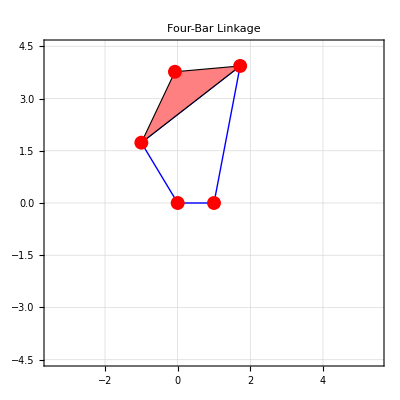

```mathematica
Show[{la1,la2,la3},PlotLabel -> "Four-Bar Linkage",PlotRange->{{-3.5,5.5},{-4.5,4.5}},Frame->True,GridLines->Automatic]
(* 
這邊是將三個圖形一起呈現出來
PlotLabel -> "Four-Bar Linkage"  這個是將 圖片的名稱 填入 我們設定的  與前面的填充很雷同

PlotRange->{{-3.5,5.5},{-4.5,4.5}} 這是設定圖片顯示的座標範圍，如果沒有填寫就是看圖片多大就顯示多大，可以拿掉這段試試看

Frame->True  開啟邊寬

GridLines->Automatic  格線 自動
*)
```

# 2. Animation

## 2.1 Input set of angle 2

```mathematica
nump=101; (* 這個變數應該是設定有幾個分割點的意思(可以自行調整老師原用10，但為了更順暢我改為101)，但我不知道這個變數的命名是以哪個英文的縮寫，number of points? *)
```

```mathematica
Ang2={0,2π};(* 設定動畫中二桿的旋轉範圍*)
```

```mathematica
AngSet2=Table[Ang2[[1]]+(Ang2[[2]]-Ang2[[1]])/(nump-1)*(k-1),{k,1,nump}]//N;
(* 旋轉角度的切段，Table有點類似之前學過的陣列Array，Mathemetica裡面也有Array但我沒有去研究
   各項內容說明：
	   Ang2[[1]]：Ang2第一項，定義為初始位置，這邊值為0
	  Ang2[[2]]：Ang2第二項，定義為中指位置，這邊值為2π
	 nump - 1 ：定義為有幾個區間，例如10個人中間有9個空位的意思
		
     (Ang2[[2]]-Ang2[[1]])/(nump-1):以上合併出來的這一項為每一個區間的長度，像是數列1~10，分成9個區間，每個區間長度為1
		
	(k-1),{k,1,nump}這部分可能要幾個利題材比較好懂
	Table[k,{k,1,10}] 這樣的話結果會是 {1,2,3,4,5,6,7,8,9,10}
	所以Table[(k-1),{k,1,nump}] 姊果會是 {0,1,2,3......nump}
	所以邊的意思合併 初始位置(Ang2[[1]]) + 區間長度((Ang2[[2]]-Ang2[[1]])/(nump-1))*第幾個區段[(k-1)] 
	就是每一個區間的絕對位置的意思。
		一步一步來執行：(假設區間長度為X)
			k=1：
				初始位置(0)+區間長度(X)*第0個區段(1-1) = 0
		   k=2：
				初始位置(0)+區間長度(X)*第1個區段(2-1) = 1X
		   k=3：
				初始位置(0)+區間長度(X)*第2個區段(3-1) = 2X
					......blabla
		   k=nump：
				初始位置(0)+區間長度(X)*第nump-1個區段(nump-1) = (nump-1)X = 2π

補充  //N 為轉為小數的意思			
			(1/3) 結果為 1/3，(1/3)//N結果為0.3333
*)
```

## 2.2 All angles

### Angle 1

```mathematica
AngSet1=Table[vtheta1,{k,1,nump}];
(*將每個區段對應的角度1放入 AngSet1 這個變數*)
```

### Angle 4

```mathematica
AngSet4=Table[theta4/.{Subscript[θ, 1]-> vtheta1,Subscript[θ, 2]-> AngSet2[[k]]},{k,1,nump}];
(*將每個區段對應的角度4放入 AngSet4 這個變數
因為角度4與旋轉的角度2有關係，所以在應用時要找到對應區段的角度值
*)
```

### Angle 3

```mathematica
AngSet3=Table[theta3/.{Subscript[θ, 1]-> vtheta1,Subscript[θ, 2]-> AngSet2[[k]],Subscript[θ, 4]-> AngSet4[[k]]},{k,1,nump}];
```

```mathematica
(*同上*)
```

### Angle 7

```mathematica
AngSet7=Table[AngSet3[[k]],{k,1,nump}];
```

```mathematica
(*同上*)
```

### Angle 8

```mathematica
AngSet8=Table[AngSet3[[k]]+π/2,{k,1,nump}];
(*同上*)
```

### Allang

```mathematica
AllAngSet=Table[{Subscript[θ, 1]->AngSet1[[k]] ,Subscript[θ, 2]-> AngSet2[[k]],Subscript[θ, 3]-> AngSet3[[k]],Subscript[θ, 4]-> AngSet4[[k]],Subscript[θ, 7]-> AngSet7[[k]],Subscript[θ, 8]-> AngSet8[[k]]},{k,1,nump}];
(*是前面提過的每個角度的變數對應的真值，其餘對應方式同上*)
```

```mathematica
AllAngSet[[1]]
```

{θ_1→0,θ_2→0.,θ_3→-1.16706,θ_4→-0.935085,θ_7→-1.16706,θ_8→0.403736}

```mathematica
(*展示第一個區段的對應的角度值*)
```

## 2.3 All positions

```mathematica
AllPosi1=Table[{r0A,rA,rB,r0B,r0A}/.AllAngSet[[k]],{k,1,nump}];
```

```mathematica
AllPosi2=Table[{rA,rB,rE}/.AllAngSet[[k]],{k,1,nump}];
```

```mathematica
AllPosi3=Table[{r0A,rA,rB,r0B,rE}/.AllAngSet[[k]],{k,1,nump}];
```

```mathematica
AllPosi1[[1]]
```

{{0,0},{2.,0.},{3.375,-3.2186},{1.,0.},{0,0}}

```mathematica
AllPosi2[[1]]
```

{{2.,0.},{3.375,-3.2186},{3.70531,-1.44634}}

```mathematica
AllPosi3[[1]]
```

{{0,0},{2.,0.},{3.375,-3.2186},{1.,0.},{3.70531,-1.44634}}

## 2.4 Plot All positions

```mathematica
laSet1=Table[Graphics[{Blue,Thick,Line[AllPosi1[[k]]]}],{k,1,nump}];
(*畫線，增加多個區段的圖*)
```

```mathematica
laSet2=Table[Graphics[{EdgeForm[{Black,Thick}],Pink,Polygon[AllPosi2[[k]]]}],{k,1,nump}];
(*畫多邊形，增加多個區段的圖*)
```

```mathematica
laSet3=Table[Graphics[{Red,PointSize[0.025],Point[AllPosi3[[k]]]}],{k,1,nump}];
(*畫點，增加多個區段的圖*)
```

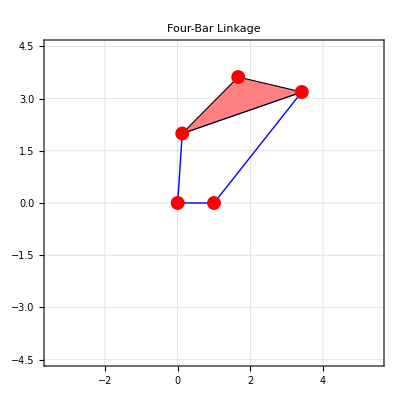

```mathematica
k=25;
Show[{laSet1[[k]],laSet2[[k]],laSet3[[k]]},PlotLabel -> "Four-Bar Linkage",PlotRange->{{-3.5,5.5},{-4.5,4.5}},Frame->True,GridLines->Automatic]
(* 合併，展示在k = 25這個區段的圖 *)
```

## 2.5 Animate

```mathematica
Animate[Show[{laSet1[[k]],laSet2[[k]],laSet3[[k]]},PlotLabel -> "Four-Bar Linkage",PlotRange->{{-3.5,5.5},{-4.5,4.5}},Frame->True,GridLines->Automatic],{k,1,nump,1},AnimationRunning->False]
(*動畫的函式，Animate應用在不同的場合有不同的參數填寫方法，這邊講其中一個基本的
Animate[expr,{u,umin,umax}]，以下把這個函式分長三個部分


Animate[

Show[{laSet1[[k]],laSet2[[k]],laSet3[[k]]},PlotLabel -> "Four-Bar Linkage",PlotRange->{{-3.5,5.5},{-4.5,4.5}},Frame->True,GridLines->Automatic],

{k,1,nump,1},

AnimationRunning->False
]

第一個就是：expr就是我們畫圖呈現的東西
		expr裡面填的和前面合併三個圖是一樣的，只是一樣改成多個區段的變數值(k)，

 第二個就是：u就是每張圖變動所更動的值，umin、umax很明顯知道是甚麼了
	u填寫的是{k,1,nump,1} 代表k 從 1跑到大於nump每次更動量為1 ，有點像其他語言的for迴圈的條件值
	動畫裡面出現可以調整的k是因為我們可以應用的部分是 k

第三個比較特別是動畫的額外參數：
	是在指定動畫的參數，是說明這個動畫不要自動開始執行，也可以拿掉試試看是不是這樣。


*)
```